# Hadamard _s Ū of the BPT Green function in ℳ_2

This notebook is based on the supplemental material provided in PRD 100, 104037 (2019). Besides the calculation of Synge’s world function σ̄ in ℳ_2, we also provide a small coordinate expansion for the Biscalar _s Ū, which satisfies the transport equation

(2(σ̄)^i∇_i + □σ̄ - 2 + 2s a^i(σ̄)_i)_s Ū=0

## Spacetime

ⅆ s^2=-f[r]/r^2ⅆ t^2+1/(f[r]r^2)ⅆ r^2

```mathematica
nMax=22; (* order for σ̄ *)
f[r_]=1-(2M)/r;
Subscript[g, t,t][r_]=-f[r]/r^2;
Subscript[g, r,r][r_]=1/(f[r] r^2);
sqrtDetG[r_]=1/r^2;
```

dt = t - t'
dr = r - r'

### Small coordinate expansion for σ̄

```mathematica
Clear@σCoefγ
σCoefγ[0,0][r_]=0; 
σCoefγ[2,0][r_]=(Subscript[g, t,t][r])/2;
σCoefγ[0,2][r_]=(Subscript[g, r,r][r])/2;
Do[σCoefγ[2i+1,_][r_]=0,{i,0,nMax/2}];
```

```mathematica
σExp=0;
σExtra=0;
nCurrent=2;
Do[If[i+k>= 2 && i+k<=nCurrent,σExp=σExp+σCoefγ[i,k][r] ϵ^(i+k) dt^i dr^k],{i,0,nCurrent},{k,0,nCurrent}];
σSumt=1/ϵ D[σExp, dt];(* Subscript[σ̄, t]=(∂σ̄)/(∂dt)ⅆdt/ⅆt=1/ϵ(∂σ̄)/(∂dt), the 1/ϵ corrects the order in Subscript[σ̄, t] (differentiation reduces the order of the expansion) *)
σSumr=D[σExp, r]+1/ϵ D[σExp, dr]; (* Subscript[σ̄, r]=(∂σ̄)/(∂r)+(∂σ̄)/(∂dr)ⅆr/ⅆdr=(∂σ̄)/(∂r)+1/ϵ(∂σ̄)/(∂dr), the 1/ϵ corrects the order in Subscript[σ̄, t] (differentiation reduces the order of the expansion) *)
```

```mathematica
(* Solving (σ̄)^i Subscript[σ̄, i]=2 σ̄ *)

While[nCurrent<nMax,
nCurrent=nCurrent+1;
σExtra=0;
Do[If[i+k>= 2 && i+k==nCurrent,σExtra=σExtra+σCoefγ[i,k][r] ϵ^(i+k) dt^i dr^k],{i,0,nCurrent},{k,0,nCurrent}];
σExp=σExp+σExtra;
σSumt=σSumt+1/ϵ D[σExtra, dt];
σSumr=σSumr+D[σExtra, r]+1/ϵ D[σExtra, dr];
σEqn=Coefficient[1/(Subscript[g, t,t][r]) Series[σSumt^2,{ϵ,0,nMax}]+1/(Subscript[g, r,r][r]) Series[σSumr^2,{ϵ,0,nMax}]-2 σExp,ϵ,nCurrent];
Print[nCurrent,"\t",Timing[Do[tmp=σCoefγ[i,nCurrent-i][r]/.Solve[Coefficient[σEqn,dt^i dr^(nCurrent-i)]==0,σCoefγ[i,nCurrent-i][r]][[1]];
σCoefγ[i,nCurrent-i][r_]=Simplify[tmp]
,{i,0,nCurrent,2}]][[1]],"\t",Floor[MemoryInUse[]/1024]];];
```

3	0.00704	159231

4	0.015618	158928

5	0.016765	158850

6	0.035677	158500

7	0.081417	158200

8	0.157762	157847

9	0.374399	157700

10	0.606846	157708

11	1.30128	157827

12	2.10476	157434

```mathematica
σ=σExp;
Subscript[σ, t]=1/ϵ D[σ, dt];
Subscript[σ, r]=D[σ, r]+1/ϵ D[σ, dr];
```

```mathematica
Boxσ=1/(Subscript[g, t,t][r])1/ϵ^2 D[σ, dt,dt]+With[{tmp=sqrtDetG[r]/(Subscript[g, r,r][r]) Subscript[σ, r]},1/sqrtDetG[r](D[tmp, r]+1/ϵ D[tmp, dr])];
```

```mathematica
Boxσ+O[ϵ]^2
```

2+O[ϵ]^2

### Small coordinate expansion for _s Ū

```mathematica
(* Solving Subscript[(2(σ̄)^i∇_i + □σ̄ - 2 + 2 s a^i Subscript[σ̄, i]), s] Ū=0 *)

sUNMax=nMax-2; (* order for _s Ū *)
Clear[sUCoef]

sUCoef[i_,_][r_]/;i>sUNMax=0;
sUCoef[0,0][r_]=1;

at=-r/f[r](1-(3M)/r);
ar=r-M;

sUExp=Module[{U0Sum=0},Do[If[i+k>=0 && i+k<=sUNMax,U0Sum=U0Sum+sUCoef[i,k][r] ϵ^(i+k) dt^i dr^k],{i,0,sUNMax},{k,0,sUNMax}];U0Sum];
Clear@sUEqns
sUEqns=CoefficientList[
1/(Subscript[g, t,t][r]) Series[1/ϵ Subscript[σ, t] D[sUExp, dt],{ϵ,0,sUNMax}]
+1/(Subscript[g, r,r][r])Series[Subscript[σ, r] (D[sUExp, r]+1/ϵ D[sUExp, dr]),{ϵ,0,sUNMax}]
+1/2 Series[(Boxσ-2 + 2s at Subscript[σ, t] + 2 s ar Subscript[σ, r])sUExp,{ϵ,0,sUNMax}],
ϵ
];
```

```mathematica
Monitor[
Do[
Do[
tmp=sUCoef[i,order-i][r]/.Solve[Coefficient[sUEqns[[order+1]],dt^i dr^(order-i)]==0,sUCoef[i,order-i][r]][[1]];
sUCoef[i,order-i][r_]=Simplify[tmp,Assumptions->{s∈Integers,M>1,r>2M}],
{i,0,order}
],
{order,1,sUNMax}
]
,
{i,order}
]
```

```mathematica
sU=Module[{U0Sum=0},Do[If[i+k>= 0 && i+k<=sUNMax,U0Sum=U0Sum+sUCoef[i,k][r] ϵ^(i+k) dt^i dr^k],{i,0,sUNMax},{k,0,sUNMax}];U0Sum];
```

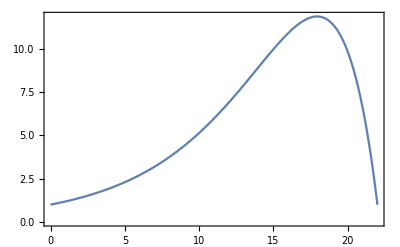

```mathematica
Block[{U,sU10,s=-2,dr=0,r=6,M=1},
U=sU/.{ϵ->1};
Plot[{U},{dt,0,22},Frame->True]
]
```